#### Figure 3

```mathematica
params1 = { mubar-> 2.26*10^(-2), ga-> 0.52,gm-> 0.411,gb-> 8.33*10^(-4), k-> 7200.,n-> 2.,  k1-> 2.52*10^(4),am-> 9.97*10^(-4),gamma0-> 7.25*10^(-7),ab-> 1.66*10^(-2),aa-> 1.76*10^(4), ba-> 2.15*10^(4),kl-> 0.97,ka-> 1.95, taum-> 0.1, taub -> 2.12, gl-> 0.0,  gp-> 0.65 ,al-> 2880., ap-> 10., bl1-> 2.65*10^(3),kle-> 0.26, kl1-> 1.81, taup-> 0.83,  kl2-> 0.97, bl2-> 1.76*10^(4), Le-> 8.*10^(-2),mumax-> 3.47 *10^(-2)};
```

```mathematica
sol2 = NDSolve[
{M'[t] == am*(1+k1*(Exp[-mubar*taum]*A[t-taum])^n)/(k+k1*(Exp[-mubar*taum]*A[t-taum])^n)+gamma0-(gm+mubar)*M[t],

B'[t] == ab*Exp[-mubar*taub]*M[t-taub]-(gb+mubar)*B[t],

A'[t] == aa*B[t]*L[t]/(kl+L[t])-ba*B[t]*A[t]/(ka+A[t])-(ga+mubar)*A[t],
L'[t] == al*P[t]*Le/(kle+Le) - bl1*P[t]*L[t]/(kl1+L[t])-bl2*B[t]*L[t]/(kl2+L[t]) -(gl+mubar)*L[t],
P'[t] == ap*Exp[-mubar*(taup+taub)]*M[t-(taup+taub)]-(gp+mubar)*P[t],

M[t/; t≤0]== 6.26*10^(-4), B[t/; t≤0]== 0.0, A[t/; t≤0]== 3.80*10^(-2), L[t/; t≤0]== 3.72*10^(-1), P[t/; t≤0]== 1.49*10^(-2)}/. params1,
{M[t], B[t], A[t], L[t], P[t] },{t,0,200}]
```

{{M[t]→InterpolatingFunction[…][t],B[t]→InterpolatingFunction[…][t],A[t]→InterpolatingFunction[…][t],L[t]→InterpolatingFunction[…][t],P[t]→InterpolatingFunction[…][t]}}

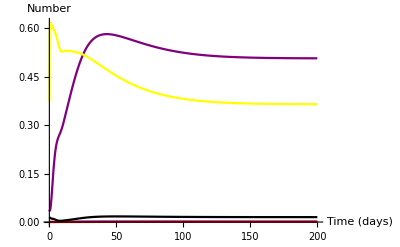

```mathematica
Plot[Evaluate[{M[t], B[t], A[t], L[t], P[t] }/.sol2],{t,0,200},PlotRange->Automatic, PlotStyle->{Blue,Red,Purple, Yellow, Black, Green},AxesLabel-> {"Time (days)", "Number"}]
```

```mathematica
B[t]/.sol2[[1]]
```

InterpolatingFunction[…][t]

```mathematica
maxB = FindMaximum[{B[t]/.sol2[[1, 2]], 0≤t≤200}, {t,80}]
```

{0.000731407,{t→174.804}}

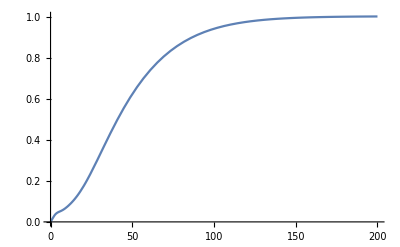

```mathematica
Plot[(B[t]/.sol2[[1,2]])/maxB[[1]] ,{t,0,200}]
```

#### Figure 4

```mathematica
paramtest = {mubar-> 2.26*10^-2,gammaA -> 5.2*10^-1,gammaM -> 0.411,gammaB -> 8.33*10^-4,k ->7200,n->2,K1->2.52*10^4,alphaM->9.97*10^-4,Gamma0->7.25*10^-7,alphaB->1.66*10^-2,alphaA->1.76*10^4,betaA->2.15*10^4,KL->1.4,KA->1.95,tauM->0.1,tauB->2.12,gammaL->0,gammaP->0.65,alphaL->2880,alphaP->10.0,betaL1->2650,KLe->2.6*10^-1,KL1->1.81,tauP->0.83,KL2->9.7*10^-1,betaL2->1.76*10^4,Le->8.0*10^-2,T-> 110};
```

```mathematica
alpha = mubar/T;
```

```mathematica
muFeeding= (mubar - alpha*Mod[t,T])
```

mubar-(mubar Mod[t,T])/T

```mathematica
sol4= NDSolve[{M'[t]==alphaM*(1+K1(E^(-muFeeding*tauM)*A[t-tauM])^n)/(k+K1(E^(-muFeeding*tauM)*A[t-tauM])^n)+Gamma0-(gammaM+muFeeding)*M[t],

 B'[t]==alphaB*E^(-muFeeding*tauB)*M[t-tauB]-(gammaB+muFeeding)*B[t],

 A'[t]==alphaA*B[t]*L[t]/(KL+L[t])-betaA*B[t]*A[t]/(KA+A[t])-(gammaA+muFeeding)*A[t],

L'[t]==alphaL*P[t]*Le/(KLe+Le)-betaL1*P[t]*L[t]/(KL1+L[t])-betaL2*B[t]*L[t]/(KL2+L[t])-(gammaL+muFeeding)*L[t],
 P'[t]==alphaP*E^(-muFeeding*(tauP+tauB))*M[t-(tauP+tauB)]-(gammaP+muFeeding)*P[t],


M[t/; t≤0]== 6.26*10^(-4), B[t/; t≤0]== 0.0, A[t/; t≤0]== 3.80*10^(-2), L[t/; t≤0]== 3.72*10^(-1), P[t/; t≤0]== 1.49*10^(-2)} /. paramtest, {M[t], B[t], A[t], L[t], P[t]},{t, 180, 380}];
```

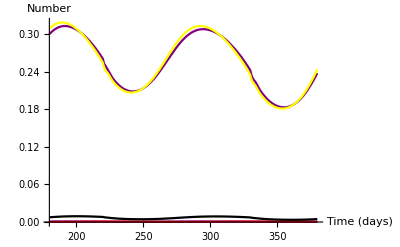

```mathematica
Plot[Evaluate[{M[t], B[t], A[t], L[t], P[t] }/.sol4],{t,180,380},PlotRange->Automatic, PlotStyle->{Blue,Red,Purple, Yellow, Black, Green},AxesLabel-> {"Time (days)", "Number"}]
```

```mathematica
maxB2=FindMaximum[{B[t]/.sol4[[1, 2]], 180≤t≤380}, {t, 200}]
```

{0.000778859,{t→220.}}

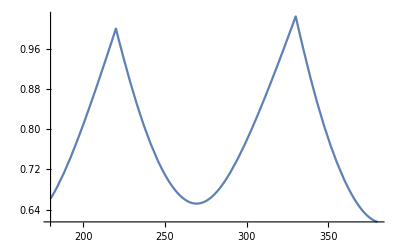

```mathematica
Plot[(B[t]/.sol4[[1,2]])/maxB2[[1]] ,{t,180,380}]
```

```mathematica
(*ERROR For Some Reason*)
```

```mathematica
params2 = { mubar-> 2.26*10^(-2), ga-> 0.52,gm-> 0.411,gb-> 8.33*10^(-4), k-> 7200.,n-> 2.,  k1-> 2.52*10^(4),am-> 9.97*10^(-4),gamma0-> 7.25*10^(-7),ab-> 1.66*10^(-2),aa-> 1.76*10^(4), ba-> 2.15*10^(4),kl-> 0.97,ka-> 1.95, taum-> 0.1, taub -> 2.12, gl-> 0.0,  gp-> 0.65 ,al-> 2880., ap-> 10., bl1-> 2.65*10^(3),kle-> 0.26, kl1-> 1.81, taup-> 0.83,  kl2-> 0.97, bl2-> 1.76*10^(4), Le-> 8.*10^(-2),mumax-> 3.47 *10^(-2), per-> 110}
```

{mubar→0.0226,ga→0.52,gm→0.411,gb→0.000833,k→7200.,n→2.,k1→25200.,am→0.000997,gamma0→7.25×10^-7,ab→0.0166,aa→17600.,ba→21500.,kl→0.97,ka→1.95,taum→0.1,taub→2.12,gl→0.,gp→0.65,al→2880.,ap→10.,bl1→2650.,kle→0.26,kl1→1.81,taup→0.83,kl2→0.97,bl2→17600.,Le→0.08,mumax→0.0347,per→110}

```mathematica
alpha = mubar/per;
```

```mathematica
muFeed= (mubar - alpha*Mod[t,per])
```

mubar-(mubar Mod[t,per])/per

```mathematica
sol3 = NDSolve[
{M'[t] == am*(1+k1*(Exp[-muFeed*taum]*A[t-taum])^n)/(k+k1*(Exp[-muFeed*taum]*A[t-taum])^n)+gamma0-(gm+muFeed)*M[t],

B'[t] == ab*Exp[-muFeed*taub]*M[t-taub]-(gb+muFeed)*B[t],

A'[t] == aa*B[t]*L[t]/(kl+L[t])-ba*B[t]*A[t]/(ka+A[t])-(ga+muFeed)*A[t],
L'[t] == al*P[t]*Le/(kle+Le) - bl1*P[t]*L[t]/(kl1+L[t])-bl2*B[t]*L[t]/(kl2+L[t]) -(gl+muFeed)*L[t],
P'[t] == ap*Exp[-muFeed*(taup+taub)]*M[t-(taup+taub)]-(gp+muFeed)*P[t],

M[t/; t≤0]== 6.26*10^(-4), B[t/; t≤0]== 0.0, A[t/; t≤0]== 3.80*10^(-2), L[t/; t≤0]== 3.72*10^(-1), P[t/; t≤0]== 1.49*10^(-2)}/. params2,
{M[t], B[t], A[t], L[t], P[t] },{t,180,380}];
```

NDSolve::nbnum1: The function value 0.997743 Im[A$2446]==0 is not True or False when the arguments are {0.,0.038,0.,0.372,0.000626,0.0149,-0.0201894,0.0000101456,3.36111,-0.000258495,-0.00379861,1}.

NDSolve::nbnum1: The function value 0.997743 Im[A$2446]==0 is not True or False when the arguments are {0.,0.038,0.,0.372,0.000626,0.0149,-0.0206188,9.90546×10^-6,3.3569,-0.00026558,-0.00416549,1}.

NDSolve::nbnum1: The function value 0.997743 Re[A$2446]≤0 is not True or False when the arguments are {0.,0.038,0.,0.372,0.000626,0.0149,-0.0206188,9.90546×10^-6,3.3569,-0.00026558,-0.00416549,1}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

NDSolve::ecboo: The value of event condition function at t = 0. was not True or False. The event will be considered inactive.

NDSolve::ecboo: The value of event condition function at t = 0.0000102039 was not True or False. The event will be considered inactive.

NDSolve::ecboo: The value of event condition function at t = 0.0000204079 was not True or False. The event will be considered inactive.

General::stop: Further output of NDSolve::ecboo will be suppressed during this calculation.

#### Figure 5

```mathematica
funcB0[B0value_]:=Module[{params,sol},
params = { mubar-> 2.26*10^(-2), ga-> 0.52,gm-> 0.411,gb-> 8.33*10^(-4), k-> 7200.,n-> 2.,  k1-> 2.52*10^(4),am-> 9.97*10^(-4),gamma0-> 7.25*10^(-7),ab-> 1.66*10^(-2),aa-> 1.76*10^(4), ba-> 2.15*10^(4),kl-> 1.4,ka-> 1.95, taum-> 0.1, taub -> 2.12, gl-> 0.0,  gp-> 0.65 ,al-> 2880., ap-> 10., bl1-> 2.65*10^(3),kle-> 0.26, kl1-> 1.81, taup-> 0.83,  kl2-> 0.97, bl2-> 1.76*10^(4), Le-> 4.28*10^(-2),mumax-> 3.47 *10^(-2)};
sol = NDSolve[
{M'[t] == am*(1+k1*(Exp[-mubar*taum]*A[t-taum])^n)/(k+k1*(Exp[-mubar*taum]*A[t-taum])^n)+gamma0-(gm+mubar)*M[t],

B'[t] == ab*Exp[-mubar*taub]*M[t-taub]-(gb+mubar)*B[t],

A'[t] == aa*B[t]*L[t]/(kl+L[t])-ba*B[t]*A[t]/(ka+A[t])-(ga+mubar)*A[t],
L'[t] == al*P[t]*Le/(kle+Le) - bl1*P[t]*L[t]/(kl1+L[t])-bl2*B[t]*L[t]/(kl2+L[t]) -(gl+mubar)*L[t],
P'[t] == ap*Exp[-mubar*(taup+taub)]*M[t-(taup+taub)]-(gp+mubar)*P[t],

M[t/; t≤0]== 3.46*10^(-5), B[t/; t≤0]== B0value, A[t/; t≤0]== 6.43*10^(-2), L[t/; t≤0]== 1.36*10^(-1), P[t/; t≤0]== 4.83*10^(-4)}/. params,
{M[t], B[t], A[t], L[t], P[t] },{t,0,800}];
LogPlot[Evaluate[B[t]/.sol],{t,0,800},PlotRange->{{0,800},{10^-(7),10^(-3)}}, PlotStyle->Black,AxesLabel-> {"Time (days)", "Number"}]
]
```

```mathematica
initB = Range[0.24,0.32,(0.32-0.24)/4]*10^(-4)
```

{0.000024,0.000026,0.000028,0.00003,0.000032}

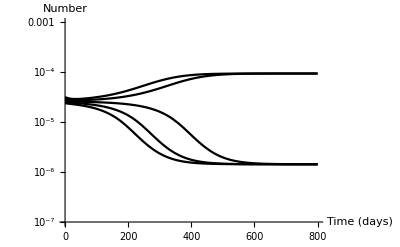

```mathematica
Show[funcB0[initB[[1]]],funcB0[initB[[2]]],funcB0[initB[[3]]],funcB0[initB[[4]]],funcB0[initB[[5]]]]
```

#### Figure 2

```mathematica
funcEq[{lepar_,Abar_}] :=Module[{params,hpar,p1par,p2par,p3par,f1,f2,f3, LAdep, h0},
params ={ mubar-> 2.26*10^(-2), ga-> 0.52,gm-> 0.411,gb-> 8.33*10^(-4), k-> 7200.,n-> 2.,  k1-> 2.52*10^(4),am-> 9.97*10^(-4),gamma0-> 7.25*10^(-7),ab-> 1.66*10^(-2),aa-> 1.76*10^(4), ba-> 2.15*10^(4),kl-> 0.97,ka-> 1.95, taum-> 0.1, taub -> 2.12, gl-> 0.0,  gp-> 0.65 ,al-> 2880., ap-> 10., bl1-> 2.65*10^(3),kle-> 0.26, kl1-> 1.81, taup-> 0.83,  kl2-> 0.97, bl2-> 1.76*10^(4)};
hpar= lepar/(kl+lepar)/.params;
p1par = (al ap Exp[-mubar*(taub+taup)]*hpar)/((gm+mubar)*(gp+mubar))/.params;
p2par =  (bl1 ap Exp[-mubar*(taub+taup)])/((gm+mubar)*(gp+mubar))/.params;
p3par = (bl2 ab Exp[-mubar*taub])/((gm+mubar)*(gb+mubar))/.params;
f1= (1+k1*Exp[-2 mubar taum] Abar^2)/(k+k1*Exp[-2 mubar taum] Abar^2)/.params;
f2= Abar/(ka+Abar)/.params;
f3= (ba ab Exp[-mubar*taub] f2(am f1+gamma0)+ (ga+mubar)(gm+mubar)(gb+mubar)Abar)/(aa ab Exp[-mubar*taub](am f1+ gamma0))/.params;
LAdep= (kl f3)/(1-f3)/.params;
h0= p1par - p2par LAdep/(kl1+LAdep)-p3par LAdep/(kl+LAdep)/.params;
(*Return[{N[h0]≥0, N[f3]≥ 0&&N[f3]<1}]*)

(*Return[{p1par,p2par,p3par, h0}]*)

If[N[h0]≥0 && N[f3]≥ 0&&N[f3]<1,Return[1], Return[0]]
]
```

```mathematica
funcEq[0.01,0.2]
```

0

```mathematica
funcEq[0.08,0.5]
```

0

```mathematica
funcEq[0.105,0.1]
```

1

```mathematica
testpts = RandomPoint[Rectangle[{0,0},{0.3,0.5}],5000];
```

```mathematica
testpts[[1]]
```

{0.0782913,0.459434}

```mathematica
vals = funcEq[#]&/@testpts;
```

```mathematica
data = Transpose[{testpts[[All,1]],testpts[[All,2]], vals}];
```

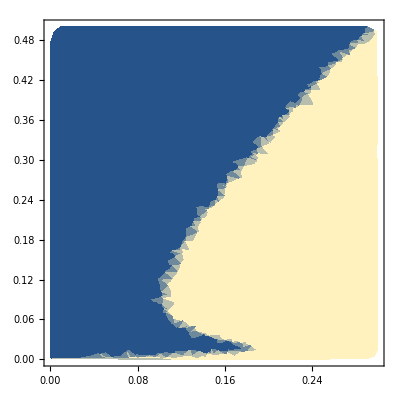

```mathematica
ListDensityPlot[data]
```

```mathematica
(*Extra if we want to solve for the line*)
(*f1[A_]:= (1+k1*Exp[-2 mubar taum] A^2)/(k0+k1*Exp[-2 mubar taum] A^2);
f2[A_]:= A/(ka+A);
f3[A_]:= (ba ab Exp[-mubar*taub] f2[A](am f1[A]+gamma0)+ (ga+mubar)(gm+mubar)(gb+mubar)A)/(aa ab Exp[-mubar*taub](am f1[A]+ gamma0));
LAdep[A_]:= (kl f3[A])/(1-f3[A]);
h0[A_]:= p1par - p2par LAdep[A]/(kl1+LAdep[A])-p3par LAdep[A]/(kl+LAdep[A]);*)
```